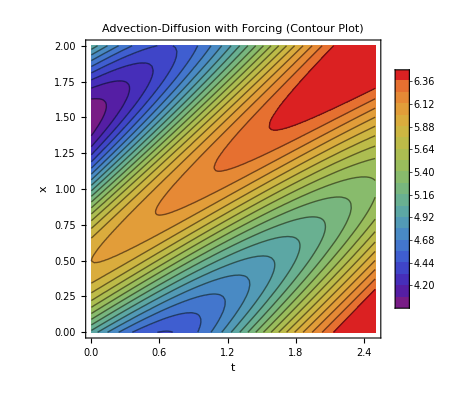

```mathematica
(*Parameters:Enter values for ax,mu,and define the range for x and t*)
ax=3/5;
mu=1/50;
xMin=0;
xMax=2;
tMin=0;
tMax=2.5;
T0=5;

(*Define the forcing term F(x,t):Insert your forcing profile here*)
F=0.4;

(*Define the advection-diffusion PDE with the forcing term*)
pde=D[u[x,t],t]==-ax*D[u[x,t],x]+mu*D[u[x,t],{x,2}]+F;

(*Initial condition:Insert your initial condition here*)
initialCondition=u[x,0]==T0+Sin[2*Pi*x/xMax];

(*Boundary conditions:periodic boundary conditions*)
boundaryConditions={u[xMin,t]==u[xMax,t],Derivative[1,0][u][xMin,t]==Derivative[1,0][u][xMax,t]};

(*Solve the PDE numerically*)
sol=NDSolve[{pde,initialCondition,boundaryConditions},u,{x,xMin,xMax},{t,tMin,tMax}];

(*Create a contour plot of the solution with a colorbar*)ContourPlot[Evaluate[u[x,t]/. sol],{t,tMin,tMax},{x,xMin,xMax},PlotLegends->Automatic,ColorFunction->"Rainbow",PlotRange->All,Contours->20,PlotLabel->"Advection-Diffusion with Forcing (Contour Plot)",AxesLabel->{"t","x"}]
```